```mathematica
For[i=0,i≤3,i++,
	For[j=0,j≤3,j++,
		f[4i+j+1]=Map[{i+1,j+1}+#&,{{0,0},{0,1},{1,1},{1,0}}]]]
```

```mathematica
For[i=0,i≤2,i++,
	For[j=0,j≤2,j++,
		f[3i+j+17]=Map[{i+1,j+1}+#&,{{0,0},{0,2},{2,2},{2,0}}]]]
```

```mathematica
For[i=0,i≤1,i++,
	For[j=0,j≤1,j++,
		f[2i+j+26]=Map[{i+1,j+1}+#&,{{0,0},{0,3},{3,3},{3,0}}]]]
```

```mathematica
f[30]={{1,1},{1,5},{5,5},{5,1}};
```

```mathematica
For[i=0,i≤2,i++,
	For[j=0,j≤2,j++,
		f[3i+j+31]=Map[{i+1,j+1}+#&,{{0,1},{1,0},{2,1},{1,2}}]]]
```

```mathematica
For[i=0,i≤1,i++,
	For[j=0,j≤1,j++,
		f[2i+j+40]=Map[{i+1,j+1}+#&,{{0,2},{1,0},{3,1},{2,3}}]]]
```

```mathematica
For[i=0,i≤1,i++,
	For[j=0,j≤1,j++,
		f[2i+j+44]=Map[{i+1,j+1}+#&,{{0,1},{2,0},{3,2},{1,3}}]]]
```

```mathematica
f[48]={{1,3},{3,1},{5,3},{3,5}};
```

```mathematica
f[49]={{1,4},{2,1},{5,2},{4,5}};
```

```mathematica
f[50]={{1,2},{4,1},{5,4},{2,5}};
```

```mathematica
For[i=1,i≤5,i++,
	For[j=1,j≤5,j++,
		F[i,j]={}]]
```

```mathematica
For[i=1, i≤50,i++,
	For[j=1,j<=4,j++,
		AppendTo[F[Apply[Sequence,f[i][[j]]]],i]]]
```

```mathematica
g[x_]:=Line[Join[x,{First[x]}]]
```

```mathematica
test:=Module[{},
		master={{Position[A,1],{}}};
sol={};
While[Length[master]>0,
	m1=master[[1]][[1]];
	m2=master[[1]][[2]];
	master=Rest[master];
	If[m1=={},AppendTo[sol,m2],
	u=Select[F[Apply[Sequence,m1[[1]]]],
			Complement[f[#],m1]=={}&] ;
	If[u=!={},
		s=Table[{Complement[m1,f[u[[j]]]],Join[m2,{u[[j]]}]},{j,1,Length[u]}];
			master=Join[master,s]]]
		];
Length[sol]==1]
```

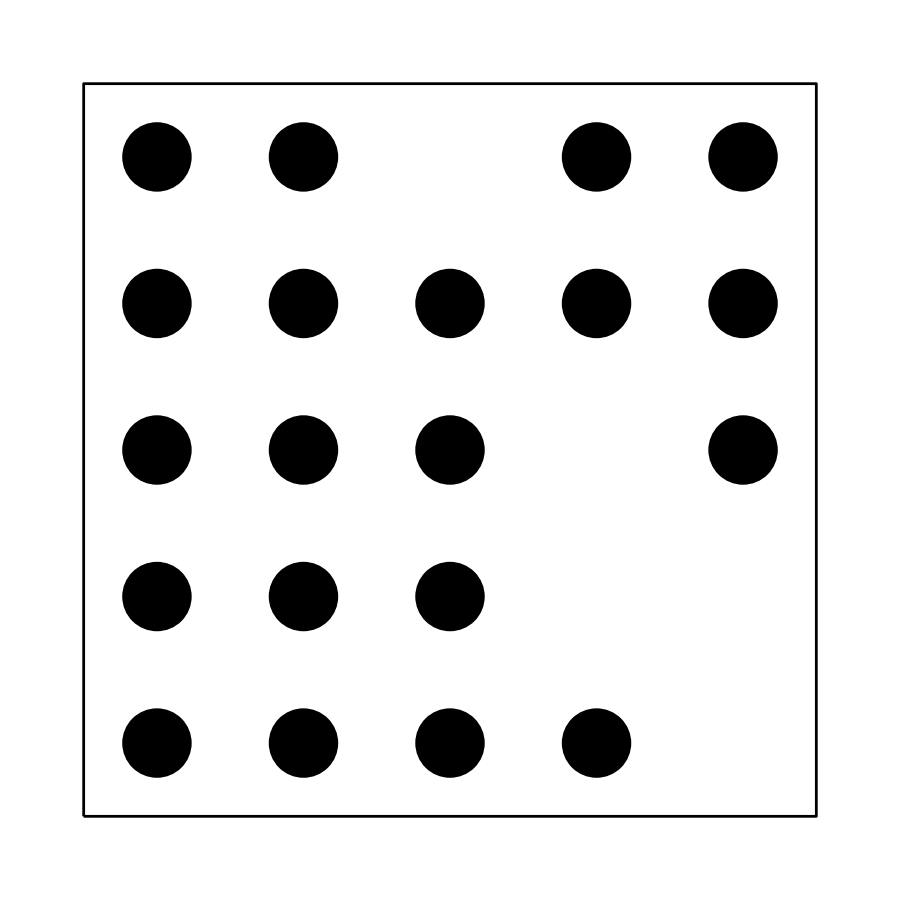

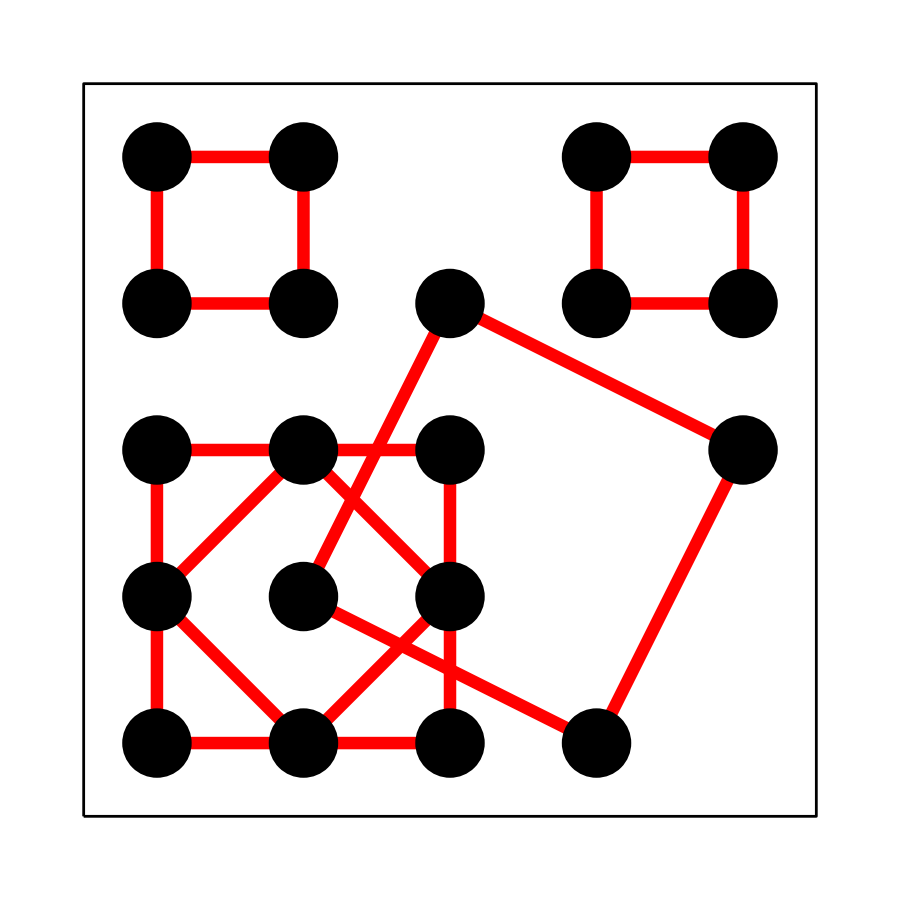

```mathematica
draw:=Module[{},Print[Style[Graphics[{AbsoluteThickness[2],Line[{{1/2,1/2},{1/2,11/2},{11/2,11/2},{11/2,1/2},{1/2,1/2}}],AbsolutePointSize[12],Point/@Position[A,1]},PlotRange->{{0.49,5.51},{0.49,5.51}},ImageSize->200],Antialiasing->False]];Print[Style[Graphics[{AbsoluteThickness[2],Line[{{1/2,1/2},{1/2,11/2},{11/2,11/2},{11/2,1/2},{1/2,1/2}}],Thickness[.01],Red,Table[g[f[B⟦i⟧]],{i,1,Length[B]}],Black,AbsolutePointSize[12],Point/@Position[A,1]},PlotRange->{{0.49,5.51},{0.49,5.51}},ImageSize->200],Antialiasing->False]]]
```

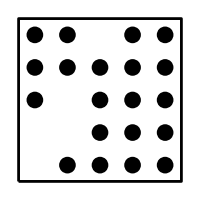

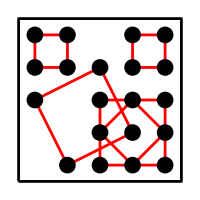

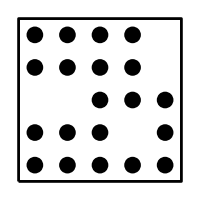

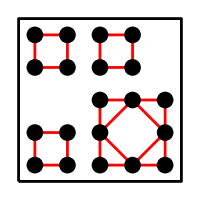

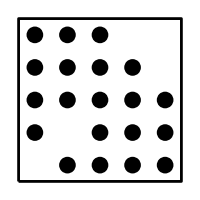

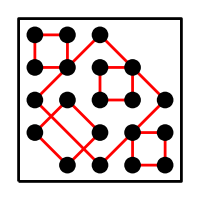

```mathematica
For[p=1,p<10,p++,A=Table[0,{5},{5}];B={};For[i=1,i≤1000,i++,r=RandomInteger[{1,50}];If[Complement[f[r],Position[A,0]]=={},AppendTo[B,r];For[j=1,j≤4,j++,A⟦Sequence@@f[r]⟦j⟧⟧=1]]];If[test&&Length[B]≥5,draw]]
```